```mathematica
Remove["CppClassLayoutParser`*"];
SetDirectory[NotebookDirectory[]];
<<"CppClassLayoutParser.wl"
```

```mathematica
classes=ParseCppToClasses["previos_exam_examples/Q2_W23-24_A.hpp"]
```

Class "X" location: <|offset→52,line→4,col→8,tokLen→1|>

Class "Y1" location: <|offset→381,line→28,col→8,tokLen→2|>

Class "Y2" location: <|offset→609,line→43,col→8,tokLen→2|>

Class "Z" location: <|offset→839,line→57,col→8,tokLen→1|>

→ FINAL classes keys: {X,Y1,Y2,Z}

<|X→<|AST→<|id→0x1300223da20,kind→CXXRecordDecl,loc→<|offset→52,line→4,col→8,tokLen→1|>,range→<|begin→<|offset→45,col→1,tokLen→6|>,end→<|offset→364,line→24,col→1,tokLen→1|>|>,isReferenced→True,name→X,tagUsed→struct,completeDefinition→True,definitionData→<|canConstDefaultInit→True,copyAssign→<|hasConstParam→True,implicitHasConstParam→True,nonTrivial→True,simple→True|>,copyCtor→<|hasConstParam→True,implicitHasConstParam→True,nonTrivial→True,simple→True|>,defaultCtor→<|exists→True,nonTrivial→True,userProvided→True|>,dtor→<|irrelevant→True,simple→True,trivial→True|>,hasUserDeclaredConstructor→True,isPolymorphic→True,moveAssign→<|exists→True,nonTrivial→True,simple→True|>,moveCtor→<|exists→True,nonTrivial→True,simple→True|>|>,inner→{<|id→0x1300223db38,kind→CXXRecordDecl,loc→<|offset→52,line→4,col→8,tokLen→1|>,range→<|begin→<|offset→45,col→1,tokLen→6|>,end→<|offset→52,col→8,tokLen→1|>|>,isImplicit→True,isReferenced→True,name→X,tagUsed→struct|>,<|id→0x1300223dbe0,kind→FieldDecl,loc→<|offset→65,line→5,col→9,tokLen→1|>,range→<|begin→<|offset→61,col→5,tokLen→3|>,end→<|offset→65,col→9,tokLen→1|>|>,isReferenced→True,name→x,type→<|qualType→int|>|>,<|id→0x1300223dce0,kind→CXXConstructorDecl,loc→<|offset→75,line→7,col→5,tokLen→1|>,range→<|begin→<|offset→75,col→5,tokLen→1|>,end→<|offset→140,line→11,col→5,tokLen→1|>|>,isUsed→True,name→X,mangledName→??0X@@QEAA@XZ,type→<|qualType→void ()|>,inner→{<|id→0x13002285ba0,kind→CompoundStmt,range→<|begin→<|offset→79,line→7,col→9,tokLen→1|>,end→<|offset→140,line→11,col→5,tokLen→1|>|>,inner→{<|id→0x1300223e810,kind→BinaryOperator,range→<|begin→<|offset→114,line→9,col→9,tokLen→1|>,end→<|offset→118,col→13,tokLen→1|>|>,type→<|qualType→int|>,valueCategory→lvalue,opcode→=,inner→{<|id→0x1300223e7b8,kind→MemberExpr,range→<|begin→<|offset→114,col→9,tokLen→1|>,end→<|offset→114,col→9,tokLen→1|>|>,type→<|qualType→int|>,valueCategory→lvalue,name→x,isArrow→True,referencedMemberDecl→0x1300223dbe0,inner→{<|id→0x1300223e7a8,kind→CXXThisExpr,range→<|begin→<|offset→114,col→9,tokLen→1|>,end→<|offset→114,col→9,tokLen→1|>|>,type→<|qualType→X *|>,valueCategory→prvalue,implicit→True|>}|>,<|id→0x1300223e7e8,kind→IntegerLiteral,range→<|begin→<|offset→118,col→13,tokLen→1|>,end→<|offset→118,col→13,tokLen→1|>|>,type→<|qualType→int|>,valueCategory→prvalue,value→7|>}|>,<|id→0x13002285ab8,kind→CXXMemberCallExpr,range→<|begin→<|offset→130,line→10,col→9,tokLen→1|>,end→<|offset→132,col→11,tokLen→1|>|>,type→<|qualType→void|>,valueCategory→prvalue,inner→{<|id→0x13002285a88,kind→MemberExpr,range→<|begin→<|offset→130,col→9,tokLen→1|>,end→<|offset→130,col→9,tokLen→1|>|>,type→<|qualType→<bound member function type>|>,valueCategory→prvalue,name→f,isArrow→True,referencedMemberDecl→0x1300223df68,inner→{<|id→0x1300223e878,kind→CXXThisExpr,range→<|begin→<|offset→130,col→9,tokLen→1|>,end→<|offset→130,col→9,tokLen→1|>|>,type→<|qualType→X *|>,valueCategory→prvalue,implicit→True|>}|>}|>}|>}|>,<|id→0x1300223de80,kind→CXXConstructorDecl,loc→<|offset→147,line→12,col→5,tokLen→1|>,range→<|begin→<|offset→147,col→5,tokLen→1|>,end→<|offset→224,line→16,col→5,tokLen→1|>|>,isUsed→True,name→X,mangledName→??0X@@QEAA@H@Z,type→<|qualType→void (int)|>,inner→{<|id→0x1300223dda8,kind→ParmVarDecl,loc→<|offset→153,line→12,col→11,tokLen→3|>,range→<|begin→<|offset→149,col→7,tokLen→3|>,end→<|offset→153,col→11,tokLen→3|>|>,isUsed→True,name→val,type→<|qualType→int|>|>,<|id→0x13002285de8,kind→CompoundStmt,range→<|begin→<|offset→158,col→16,tokLen→1|>,end→<|offset→224,line→16,col→5,tokLen→1|>|>,inner→{<|id→0x13002285d20,kind→BinaryOperator,range→<|begin→<|offset→196,line→14,col→9,tokLen→1|>,end→<|offset→200,col→13,tokLen→3|>|>,type→<|qualType→int|>,valueCategory→lvalue,opcode→=,inner→{<|id→0x13002285cb8,kind→MemberExpr,range→<|begin→<|offset→196,col→9,tokLen→1|>,end→<|offset→196,col→9,tokLen→1|>|>,type→<|qualType→int|>,valueCategory→lvalue,name→x,isArrow→True,referencedMemberDecl→0x1300223dbe0,inner→{<|id→0x13002285ca8,kind→CXXThisExpr,range→<|begin→<|offset→196,col→9,tokLen→1|>,end→<|offset→196,col→9,tokLen→1|>|>,type→<|qualType→X *|>,valueCategory→prvalue,implicit→True|>}|>,<|id→0x13002285d08,kind→ImplicitCastExpr,range→<|begin→<|offset→200,col→13,tokLen→3|>,end→<|offset→200,col→13,tokLen→3|>|>,type→<|qualType→int|>,valueCategory→prvalue,castKind→LValueToRValue,inner→{<|id→0x13002285ce8,kind→DeclRefExpr,range→<|begin→<|offset→200,col→13,tokLen→3|>,end→<|offset→200,col→13,tokLen→3|>|>,type→<|qualType→int|>,valueCategory→lvalue,referencedDecl→<|id→0x1300223dda8,kind→ParmVarDecl,name→val,type→<|qualType→int|>|>|>}|>}|>,<|id→0x13002285dc8,kind→CXXMemberCallExpr,range→<|begin→<|offset→214,line→15,col→9,tokLen→1|>,end→<|offset→216,col→11,tokLen→1|>|>,type→<|qualType→void|>,valueCategory→prvalue,inner→{<|id→0x13002285d98,kind→MemberExpr,range→<|begin→<|offset→214,col→9,tokLen→1|>,end→<|offset→214,col→9,tokLen→1|>|>,type→<|qualType→<bound member function type>|>,valueCategory→prvalue,name→f,isArrow→True,referencedMemberDecl→0x1300223df68,inner→{<|id→0x13002285d88,kind→CXXThisExpr,range→<|begin→<|offset→214,col→9,tokLen→1|>,end→<|offset→214,col→9,tokLen→1|>|>,type→<|qualType→X *|>,valueCategory→prvalue,implicit→True|>}|>}|>}|>}|>,<|id→0x1300223df68,kind→CXXMethodDecl,loc→<|offset→244,line→17,col→18,tokLen→1|>,range→<|begin→<|offset→231,col→5,tokLen→7|>,end→<|offset→297,line→20,col→5,tokLen→1|>|>,isUsed→True,name→f,mangledName→?f@X@@UEAAXXZ,type→<|qualType→void ()|>,virtual→True,inner→{<|id→0x13002285ed0,kind→CompoundStmt,range→<|begin→<|offset→248,line→17,col→22,tokLen→1|>,end→<|offset→297,line→20,col→5,tokLen→1|>|>,inner→{<|id→0x13002285eb0,kind→CXXMemberCallExpr,range→<|begin→<|offset→286,line→19,col→9,tokLen→2|>,end→<|offset→289,col→12,tokLen→1|>|>,type→<|qualType→void|>,valueCategory→prvalue,inner→{<|id→0x13002285e80,kind→MemberExpr,range→<|begin→<|offset→286,col→9,tokLen→2|>,end→<|offset→286,col→9,tokLen→2|>|>,type→<|qualType→<bound member function type>|>,valueCategory→prvalue,name→g2,isArrow→True,referencedMemberDecl→0x1300223e030,inner→{<|id→0x13002285e70,kind→CXXThisExpr,range→<|begin→<|offset→286,col→9,tokLen→2|>,end→<|offset→286,col→9,tokLen→2|>|>,type→<|qualType→X *|>,valueCategory→prvalue,implicit→True|>}|>}|>}|>}|>,<|id→0x1300223e030,kind→CXXMethodDecl,loc→<|offset→317,line→21,col→18,tokLen→2|>,range→<|begin→<|offset→304,col→5,tokLen→7|>,end→<|offset→361,line→23,col→9,tokLen→1|>|>,isUsed→True,name→g2,mangledName→?g2@X@@UEAAXXZ,type→<|qualType→void ()|>,virtual→True,inner→{<|id→0x13002285f90,kind→CompoundStmt,range→<|begin→<|offset→322,line→21,col→23,tokLen→1|>,end→<|offset→361,line→23,col→9,tokLen→1|>|>|>}|>,<|id→0x1300223e1e0,kind→CXXMethodDecl,loc→<|offset→52,line→4,col→8,tokLen→1|>,range→<|begin→<|offset→52,col→8,tokLen→1|>,end→<|offset→52,col→8,tokLen→1|>|>,isImplicit→True,name→operator=,mangledName→??4X@@QEAAAEAU0@AEBU0@@Z,type→<|qualType→X &(const X &)|>,inline→True,explicitlyDefaulted→default,inner→{<|id→0x1300223e310,kind→ParmVarDecl,loc→<|offset→52,col→8,tokLen→1|>,range→<|begin→<|offset→52,col→8,tokLen→1|>,end→<|offset→52,col→8,tokLen→1|>|>,type→<|qualType→const X &|>|>}|>,<|id→0x1300223e3f0,kind→CXXMethodDecl,loc→<|offset→52,col→8,tokLen→1|>,range→<|begin→<|offset→52,col→8,tokLen→1|>,end→<|offset→52,col→8,tokLen→1|>|>,isImplicit→True,name→operator=,mangledName→??4X@@QEAAAEAU0@$$QEAU0@@Z,type→<|qualType→X &(X &&)|>,inline→True,explicitlyDefaulted→default,inner→{<|id→0x1300223e520,kind→ParmVarDecl,loc→<|offset→52,col→8,tokLen→1|>,range→<|begin→<|offset→52,col→8,tokLen→1|>,end→<|offset→52,col→8,tokLen→1|>|>,type→<|qualType→X &&|>|>}|>,<|id→0x1300223e5c0,kind→CXXDestructorDecl,loc→<|offset→52,col→8,tokLen→1|>,range→<|begin→<|offset→52,col→8,tokLen→1|>,end→<|offset→52,col→8,tokLen→1|>|>,isImplicit→True,name→~X,mangledName→??_DX@@QEAAXXZ,type→<|qualType→void ()|>,inline→True,explicitlyDefaulted→default|>,<|id→0x13002287e88,kind→CXXConstructorDecl,loc→<|offset→52,col→8,tokLen→1|>,range→<|begin→<|offset→52,col→8,tokLen→1|>,end→<|offset→52,col→8,tokLen→1|>|>,isImplicit→True,name→X,mangledName→??0X@@QEAA@AEBU0@@Z,type→<|qualType→void (const X &)|>,inline→True,constexpr→True,explicitlyDefaulted→default,inner→{<|id→0x13002287fc0,kind→ParmVarDecl,loc→<|offset→52,col→8,tokLen→1|>,range→<|begin→<|offset→52,col→8,tokLen→1|>,end→<|offset→52,col→8,tokLen→1|>|>,type→<|qualType→const X &|>|>}|>,<|id→0x13002288048,kind→CXXConstructorDecl,loc→<|offset→52,col→8,tokLen→1|>,range→<|begin→<|offset→52,col→8,tokLen→1|>,end→<|offset→52,col→8,tokLen→1|>|>,isImplicit→True,name→X,mangledName→??0X@@QEAA@$$QEAU0@@Z,type→<|qualType→void (X &&)|>,inline→True,constexpr→True,explicitlyDefaulted→default,inner→{<|id→0x13002288180,kind→ParmVarDecl,loc→<|offset→52,col→8,tokLen→1|>,range→<|begin→<|offset→52,col→8,tokLen→1|>,end→<|offset→52,col→8,tokLen→1|>|>,type→<|qualType→X &&|>|>}|>}|>,Bases→{},Fields→{{x,int}},VTableEntries→{f,g2}|>,Y1→<|AST→<|id→0x13002285fa0,kind→CXXRecordDecl,loc→<|offset→381,line→28,col→8,tokLen→2|>,range→<|begin→<|offset→374,col→1,tokLen→6|>,end→<|offset→594,line→40,col→1,tokLen→1|>|>,isReferenced→True,name→Y1,tagUsed→struct,completeDefinition→True,definitionData→<|canConstDefaultInit→True,copyAssign→<|hasConstParam→True,implicitHasConstParam→True,nonTrivial→True,simple→True|>,copyCtor→<|hasConstParam→True,implicitHasConstParam→True,nonTrivial→True,simple→True|>,defaultCtor→<|exists→True,nonTrivial→True,userProvided→True|>,dtor→<|irrelevant→True,simple→True,trivial→True|>,hasUserDeclaredConstructor→True,isPolymorphic→True,moveAssign→<|exists→True,nonTrivial→True,simple→True|>,moveCtor→<|exists→True,nonTrivial→True,simple→True|>|>,bases→{<|access→public,isVirtual→True,type→<|qualType→X|>,writtenAccess→none|>},inner→{<|id→0x13002286110,kind→CXXRecordDecl,loc→<|offset→381,line→28,col→8,tokLen→2|>,range→<|begin→<|offset→374,col→1,tokLen→6|>,end→<|offset→381,col→8,tokLen→2|>|>,isImplicit→True,isReferenced→True,name→Y1,tagUsed→struct|>,<|id→0x13002286208,kind→CXXConstructorDecl,loc→<|offset→403,line→29,col→5,tokLen→2|>,range→<|begin→<|offset→403,col→5,tokLen→2|>,end→<|offset→460,line→32,col→5,tokLen→1|>|>,isUsed→True,name→Y1,mangledName→??0Y1@@QEAA@XZ,type→<|qualType→void ()|>,inner→{<|kind→CXXCtorInitializer,baseInit→<|qualType→X|>,inner→{<|id→0x13002288240,kind→CXXConstructExpr,range→<|begin→<|offset→409,line→29,col→11,tokLen→1|>,end→<|offset→412,col→14,tokLen→1|>|>,type→<|qualType→X|>,valueCategory→prvalue,ctorType→<|qualType→void (int)|>,hadMultipleCandidates→True,constructionKind→virtual base,inner→{<|id→0x13002286a28,kind→IntegerLiteral,range→<|begin→<|offset→411,col→13,tokLen→1|>,end→<|offset→411,col→13,tokLen→1|>|>,type→<|qualType→int|>,valueCategory→prvalue,value→2|>}|>}|>,<|id→0x130022884a8,kind→CompoundStmt,range→<|begin→<|offset→414,col→16,tokLen→1|>,end→<|offset→460,line→32,col→5,tokLen→1|>|>,inner→{<|id→0x130022883c8,kind→CXXMemberCallExpr,range→<|begin→<|offset→450,line→31,col→9,tokLen→1|>,end→<|offset→452,col→11,tokLen→1|>|>,type→<|qualType→void|>,valueCategory→prvalue,inner→{<|id→0x13002288398,kind→MemberExpr,range→<|begin→<|offset→450,col→9,tokLen→1|>,end→<|offset→450,col→9,tokLen→1|>|>,type→<|qualType→<bound member function type>|>,valueCategory→prvalue,name→f,isArrow→True,referencedMemberDecl→0x130022862d8,inner→{<|id→0x13002288388,kind→CXXThisExpr,range→<|begin→<|offset→450,col→9,tokLen→1|>,end→<|offset→450,col→9,tokLen→1|>|>,type→<|qualType→Y1 *|>,valueCategory→prvalue,implicit→True|>}|>}|>}|>}|>,<|id→0x130022862d8,kind→CXXMethodDecl,loc→<|offset→480,line→33,col→18,tokLen→1|>,range→<|begin→<|offset→467,col→5,tokLen→7|>,end→<|offset→534,line→36,col→5,tokLen→1|>|>,isUsed→True,name→f,mangledName→?f@Y1@@UEAAXXZ,type→<|qualType→void ()|>,virtual→True,inner→{<|id→0x13002288588,kind→CompoundStmt,range→<|begin→<|offset→484,line→33,col→22,tokLen→1|>,end→<|offset→534,line→36,col→5,tokLen→1|>|>,inner→{<|id→0x13002288568,kind→CXXMemberCallExpr,range→<|begin→<|offset→523,line→35,col→9,tokLen→2|>,end→<|offset→526,col→12,tokLen→1|>|>,type→<|qualType→void|>,valueCategory→prvalue,inner→{<|id→0x13002288538,kind→MemberExpr,range→<|begin→<|offset→523,col→9,tokLen→2|>,end→<|offset→523,col→9,tokLen→2|>|>,type→<|qualType→<bound member function type>|>,valueCategory→prvalue,name→g1,isArrow→True,referencedMemberDecl→0x130022863d0,inner→{<|id→0x13002288528,kind→CXXThisExpr,range→<|begin→<|offset→523,col→9,tokLen→2|>,end→<|offset→523,col→9,tokLen→2|>|>,type→<|qualType→Y1 *|>,valueCategory→prvalue,implicit→True|>}|>}|>}|>}|>,<|id→0x130022863d0,kind→CXXMethodDecl,loc→<|offset→554,line→37,col→18,tokLen→2|>,range→<|begin→<|offset→541,col→5,tokLen→7|>,end→<|offset→591,line→39,col→5,tokLen→1|>|>,isUsed→True,name→g1,mangledName→?g1@Y1@@UEAAXXZ,type→<|qualType→void ()|>,virtual→True,inner→{<|id→0x13002288640,kind→CompoundStmt,range→<|begin→<|offset→559,line→37,col→23,tokLen→1|>,end→<|offset→591,line→39,col→5,tokLen→1|>|>|>}|>,<|id→0x13002286550,kind→CXXMethodDecl,loc→<|offset→381,line→28,col→8,tokLen→2|>,range→<|begin→<|offset→381,col→8,tokLen→2|>,end→<|offset→381,col→8,tokLen→2|>|>,isImplicit→True,name→operator=,mangledName→??4Y1@@QEAAAEAU0@AEBU0@@Z,type→<|qualType→Y1 &(const Y1 &)|>,inline→True,explicitlyDefaulted→default,inner→{<|id→0x13002286680,kind→ParmVarDecl,loc→<|offset→381,col→8,tokLen→2|>,range→<|begin→<|offset→381,col→8,tokLen→2|>,end→<|offset→381,col→8,tokLen→2|>|>,type→<|qualType→const Y1 &|>|>}|>,<|id→0x13002286760,kind→CXXMethodDecl,loc→<|offset→381,col→8,tokLen→2|>,range→<|begin→<|offset→381,col→8,tokLen→2|>,end→<|offset→381,col→8,tokLen→2|>|>,isImplicit→True,name→operator=,mangledName→??4Y1@@QEAAAEAU0@$$QEAU0@@Z,type→<|qualType→Y1 &(Y1 &&)|>,inline→True,explicitlyDefaulted→default,inner→{<|id→0x13002286890,kind→ParmVarDecl,loc→<|offset→381,col→8,tokLen→2|>,range→<|begin→<|offset→381,col→8,tokLen→2|>,end→<|offset→381,col→8,tokLen→2|>|>,type→<|qualType→Y1 &&|>|>}|>,<|id→0x13002286930,kind→CXXDestructorDecl,loc→<|offset→381,col→8,tokLen→2|>,range→<|begin→<|offset→381,col→8,tokLen→2|>,end→<|offset→381,col→8,tokLen→2|>|>,isImplicit→True,name→~Y1,mangledName→??_DY1@@QEAAXXZ,type→<|qualType→void ()|>,inline→True,explicitlyDefaulted→default|>,<|id→0x1300228a3d0,kind→CXXConstructorDecl,loc→<|offset→381,col→8,tokLen→2|>,range→<|begin→<|offset→381,col→8,tokLen→2|>,end→<|offset→381,col→8,tokLen→2|>|>,isImplicit→True,name→Y1,mangledName→??0Y1@@QEAA@AEBU0@@Z,type→<|qualType→void (const Y1 &)|>,inline→True,explicitlyDefaulted→default,inner→{<|id→0x1300228a500,kind→ParmVarDecl,loc→<|offset→381,col→8,tokLen→2|>,range→<|begin→<|offset→381,col→8,tokLen→2|>,end→<|offset→381,col→8,tokLen→2|>|>,type→<|qualType→const Y1 &|>|>}|>,<|id→0x1300228a588,kind→CXXConstructorDecl,loc→<|offset→381,col→8,tokLen→2|>,range→<|begin→<|offset→381,col→8,tokLen→2|>,end→<|offset→381,col→8,tokLen→2|>|>,isImplicit→True,name→Y1,mangledName→??0Y1@@QEAA@$$QEAU0@@Z,type→<|qualType→void (Y1 &&)|>,inline→True,explicitlyDefaulted→default,inner→{<|id→0x1300228a6c0,kind→ParmVarDecl,loc→<|offset→381,col→8,tokLen→2|>,range→<|begin→<|offset→381,col→8,tokLen→2|>,end→<|offset→381,col→8,tokLen→2|>|>,type→<|qualType→Y1 &&|>|>}|>}|>,Bases→{{X,True}},Fields→{},VTableEntries→{f,g1}|>,Y2→<|AST→<|id→0x13002288650,kind→CXXRecordDecl,loc→<|offset→609,line→43,col→8,tokLen→2|>,range→<|begin→<|offset→602,col→1,tokLen→6|>,end→<|offset→826,line→55,col→1,tokLen→1|>|>,isReferenced→True,name→Y2,tagUsed→struct,completeDefinition→True,definitionData→<|canConstDefaultInit→True,copyAssign→<|hasConstParam→True,implicitHasConstParam→True,nonTrivial→True,simple→True|>,copyCtor→<|hasConstParam→True,implicitHasConstParam→True,nonTrivial→True,simple→True|>,defaultCtor→<|exists→True,nonTrivial→True,userProvided→True|>,dtor→<|irrelevant→True,simple→True,trivial→True|>,hasUserDeclaredConstructor→True,isPolymorphic→True,moveAssign→<|exists→True,nonTrivial→True,simple→True|>,moveCtor→<|exists→True,nonTrivial→True,simple→True|>|>,bases→{<|access→public,isVirtual→True,type→<|qualType→X|>,writtenAccess→none|>},inner→{<|id→0x130022887c0,kind→CXXRecordDecl,loc→<|offset→609,line→43,col→8,tokLen→2|>,range→<|begin→<|offset→602,col→1,tokLen→6|>,end→<|offset→609,col→8,tokLen→2|>|>,isImplicit→True,isReferenced→True,name→Y2,tagUsed→struct|>,<|id→0x130022888b8,kind→CXXConstructorDecl,loc→<|offset→631,line→44,col→5,tokLen→2|>,range→<|begin→<|offset→631,col→5,tokLen→2|>,end→<|offset→688,line→47,col→5,tokLen→1|>|>,isUsed→True,name→Y2,mangledName→??0Y2@@QEAA@XZ,type→<|qualType→void ()|>,inner→{<|kind→CXXCtorInitializer,baseInit→<|qualType→X|>,inner→{<|id→0x130022893a0,kind→CXXConstructExpr,range→<|begin→<|offset→637,line→44,col→11,tokLen→1|>,end→<|offset→640,col→14,tokLen→1|>|>,type→<|qualType→X|>,valueCategory→prvalue,ctorType→<|qualType→void (int)|>,hadMultipleCandidates→True,constructionKind→virtual base,inner→{<|id→0x13002289348,kind→IntegerLiteral,range→<|begin→<|offset→639,col→13,tokLen→1|>,end→<|offset→639,col→13,tokLen→1|>|>,type→<|qualType→int|>,valueCategory→prvalue,value→2|>}|>}|>,<|id→0x13002289580,kind→CompoundStmt,range→<|begin→<|offset→642,col→16,tokLen→1|>,end→<|offset→688,line→47,col→5,tokLen→1|>|>,inner→{<|id→0x130022894a0,kind→CXXMemberCallExpr,range→<|begin→<|offset→678,line→46,col→9,tokLen→1|>,end→<|offset→680,col→11,tokLen→1|>|>,type→<|qualType→void|>,valueCategory→prvalue,inner→{<|id→0x13002289470,kind→MemberExpr,range→<|begin→<|offset→678,col→9,tokLen→1|>,end→<|offset→678,col→9,tokLen→1|>|>,type→<|qualType→<bound member function type>|>,valueCategory→prvalue,name→f,isArrow→True,referencedMemberDecl→0x13002288988,inner→{<|id→0x13002289460,kind→CXXThisExpr,range→<|begin→<|offset→678,col→9,tokLen→1|>,end→<|offset→678,col→9,tokLen→1|>|>,type→<|qualType→Y2 *|>,valueCategory→prvalue,implicit→True|>}|>}|>}|>}|>,<|id→0x13002288988,kind→CXXMethodDecl,loc→<|offset→708,line→48,col→18,tokLen→1|>,range→<|begin→<|offset→695,col→5,tokLen→7|>,end→<|offset→762,line→51,col→5,tokLen→1|>|>,isUsed→True,name→f,mangledName→?f@Y2@@UEAAXXZ,type→<|qualType→void ()|>,virtual→True,inner→{<|id→0x13002289660,kind→CompoundStmt,range→<|begin→<|offset→712,line→48,col→22,tokLen→1|>,end→<|offset→762,line→51,col→5,tokLen→1|>|>,inner→{<|id→0x13002289640,kind→CXXMemberCallExpr,range→<|begin→<|offset→751,line→50,col→9,tokLen→2|>,end→<|offset→754,col→12,tokLen→1|>|>,type→<|qualType→void|>,valueCategory→prvalue,inner→{<|id→0x13002289610,kind→MemberExpr,range→<|begin→<|offset→751,col→9,tokLen→2|>,end→<|offset→751,col→9,tokLen→2|>|>,type→<|qualType→<bound member function type>|>,valueCategory→prvalue,name→g2,isArrow→True,referencedMemberDecl→0x13002288a80,inner→{<|id→0x13002289600,kind→CXXThisExpr,range→<|begin→<|offset→751,col→9,tokLen→2|>,end→<|offset→751,col→9,tokLen→2|>|>,type→<|qualType→Y2 *|>,valueCategory→prvalue,implicit→True|>}|>}|>}|>}|>,<|id→0x13002288a80,kind→CXXMethodDecl,loc→<|offset→782,line→52,col→18,tokLen→2|>,range→<|begin→<|offset→769,col→5,tokLen→7|>,end→<|offset→823,line→54,col→5,tokLen→1|>|>,isUsed→True,name→g2,mangledName→?g2@Y2@@UEAAXXZ,type→<|qualType→void ()|>,virtual→True,inner→{<|id→0x13002289698,kind→CompoundStmt,range→<|begin→<|offset→787,line→52,col→23,tokLen→1|>,end→<|offset→823,line→54,col→5,tokLen→1|>|>|>}|>,<|id→0x13002288c00,kind→CXXMethodDecl,loc→<|offset→609,line→43,col→8,tokLen→2|>,range→<|begin→<|offset→609,col→8,tokLen→2|>,end→<|offset→609,col→8,tokLen→2|>|>,isImplicit→True,name→operator=,mangledName→??4Y2@@QEAAAEAU0@AEBU0@@Z,type→<|qualType→Y2 &(const Y2 &)|>,inline→True,explicitlyDefaulted→default,inner→{<|id→0x13002288d30,kind→ParmVarDecl,loc→<|offset→609,col→8,tokLen→2|>,range→<|begin→<|offset→609,col→8,tokLen→2|>,end→<|offset→609,col→8,tokLen→2|>|>,type→<|qualType→const Y2 &|>|>}|>,<|id→0x13002289088,kind→CXXMethodDecl,loc→<|offset→609,col→8,tokLen→2|>,range→<|begin→<|offset→609,col→8,tokLen→2|>,end→<|offset→609,col→8,tokLen→2|>|>,isImplicit→True,name→operator=,mangledName→??4Y2@@QEAAAEAU0@$$QEAU0@@Z,type→<|qualType→Y2 &(Y2 &&)|>,inline→True,explicitlyDefaulted→default,inner→{<|id→0x130022891b0,kind→ParmVarDecl,loc→<|offset→609,col→8,tokLen→2|>,range→<|begin→<|offset→609,col→8,tokLen→2|>,end→<|offset→609,col→8,tokLen→2|>|>,type→<|qualType→Y2 &&|>|>}|>,<|id→0x13002289250,kind→CXXDestructorDecl,loc→<|offset→609,col→8,tokLen→2|>,range→<|begin→<|offset→609,col→8,tokLen→2|>,end→<|offset→609,col→8,tokLen→2|>|>,isImplicit→True,name→~Y2,mangledName→??_DY2@@QEAAXXZ,type→<|qualType→void ()|>,inline→True,explicitlyDefaulted→default|>,<|id→0x1300228a7d8,kind→CXXConstructorDecl,loc→<|offset→609,col→8,tokLen→2|>,range→<|begin→<|offset→609,col→8,tokLen→2|>,end→<|offset→609,col→8,tokLen→2|>|>,isImplicit→True,name→Y2,mangledName→??0Y2@@QEAA@AEBU0@@Z,type→<|qualType→void (const Y2 &)|>,inline→True,explicitlyDefaulted→default,inner→{<|id→0x1300228a910,kind→ParmVarDecl,loc→<|offset→609,col→8,tokLen→2|>,range→<|begin→<|offset→609,col→8,tokLen→2|>,end→<|offset→609,col→8,tokLen→2|>|>,type→<|qualType→const Y2 &|>|>}|>,<|id→0x1300228a998,kind→CXXConstructorDecl,loc→<|offset→609,col→8,tokLen→2|>,range→<|begin→<|offset→609,col→8,tokLen→2|>,end→<|offset→609,col→8,tokLen→2|>|>,isImplicit→True,name→Y2,mangledName→??0Y2@@QEAA@$$QEAU0@@Z,type→<|qualType→void (Y2 &&)|>,inline→True,explicitlyDefaulted→default,inner→{<|id→0x1300228aad0,kind→ParmVarDecl,loc→<|offset→609,col→8,tokLen→2|>,range→<|begin→<|offset→609,col→8,tokLen→2|>,end→<|offset→609,col→8,tokLen→2|>|>,type→<|qualType→Y2 &&|>|>}|>}|>,Bases→{{X,True}},Fields→{},VTableEntries→{f,g2}|>,Z→<|AST→<|id→0x130022896a8,kind→CXXRecordDecl,loc→<|offset→839,line→57,col→8,tokLen→1|>,range→<|begin→<|offset→832,col→1,tokLen→6|>,end→<|offset→1046,line→69,col→1,tokLen→1|>|>,name→Z,tagUsed→struct,completeDefinition→True,definitionData→<|canConstDefaultInit→True,copyAssign→<|hasConstParam→True,implicitHasConstParam→True,nonTrivial→True,simple→True|>,copyCtor→<|hasConstParam→True,implicitHasConstParam→True,needsImplicit→True,nonTrivial→True,simple→True|>,defaultCtor→<|exists→True,nonTrivial→True,userProvided→True|>,dtor→<|irrelevant→True,simple→True,trivial→True|>,hasUserDeclaredConstructor→True,isPolymorphic→True,moveAssign→<|exists→True,nonTrivial→True,simple→True|>,moveCtor→<|exists→True,needsImplicit→True,nonTrivial→True,simple→True|>|>,bases→{<|access→public,type→<|qualType→Y1|>,writtenAccess→none|>,<|access→public,type→<|qualType→Y2|>,writtenAccess→none|>},inner→{<|id→0x13002289860,kind→CXXRecordDecl,loc→<|offset→839,line→57,col→8,tokLen→1|>,range→<|begin→<|offset→832,col→1,tokLen→6|>,end→<|offset→839,col→8,tokLen→1|>|>,isImplicit→True,isReferenced→True,name→Z,tagUsed→struct|>,<|id→0x13002289958,kind→CXXConstructorDecl,loc→<|offset→857,line→58,col→5,tokLen→1|>,range→<|begin→<|offset→857,col→5,tokLen→1|>,end→<|offset→910,line→61,col→5,tokLen→1|>|>,name→Z,mangledName→??0Z@@QEAA@XZ,type→<|qualType→void ()|>,inner→{<|kind→CXXCtorInitializer,baseInit→<|qualType→X|>,inner→{<|id→0x1300228a378,kind→CXXConstructExpr,range→<|begin→<|offset→857,line→58,col→5,tokLen→1|>,end→<|offset→857,col→5,tokLen→1|>|>,type→<|qualType→X|>,valueCategory→prvalue,ctorType→<|qualType→void ()|>,hadMultipleCandidates→True,constructionKind→virtual base|>}|>,<|kind→CXXCtorInitializer,baseInit→<|qualType→Y1|>,inner→{<|id→0x1300228a780,kind→CXXConstructExpr,range→<|begin→<|offset→857,col→5,tokLen→1|>,end→<|offset→857,col→5,tokLen→1|>|>,type→<|qualType→Y1|>,valueCategory→prvalue,ctorType→<|qualType→void ()|>,hadMultipleCandidates→True,constructionKind→non-virtual base|>}|>,<|kind→CXXCtorInitializer,baseInit→<|qualType→Y2|>,inner→{<|id→0x1300228ab90,kind→CXXConstructExpr,range→<|begin→<|offset→857,col→5,tokLen→1|>,end→<|offset→857,col→5,tokLen→1|>|>,type→<|qualType→Y2|>,valueCategory→prvalue,ctorType→<|qualType→void ()|>,hadMultipleCandidates→True,constructionKind→non-virtual base|>}|>,<|id→0x1300228ad88,kind→CompoundStmt,range→<|begin→<|offset→861,col→9,tokLen→1|>,end→<|offset→910,line→61,col→5,tokLen→1|>|>,inner→{<|id→0x1300228aca8,kind→CXXMemberCallExpr,range→<|begin→<|offset→896,line→60,col→9,tokLen→1|>,end→<|offset→898,col→11,tokLen→1|>|>,type→<|qualType→void|>,valueCategory→prvalue,inner→{<|id→0x1300228ac78,kind→MemberExpr,range→<|begin→<|offset→896,col→9,tokLen→1|>,end→<|offset→896,col→9,tokLen→1|>|>,type→<|qualType→<bound member function type>|>,valueCategory→prvalue,name→f,isArrow→True,referencedMemberDecl→0x13002289a28,inner→{<|id→0x1300228ac68,kind→CXXThisExpr,range→<|begin→<|offset→896,col→9,tokLen→1|>,end→<|offset→896,col→9,tokLen→1|>|>,type→<|qualType→Z *|>,valueCategory→prvalue,implicit→True|>}|>}|>}|>}|>,<|id→0x13002289a28,kind→CXXMethodDecl,loc→<|offset→930,line→62,col→18,tokLen→1|>,range→<|begin→<|offset→917,col→5,tokLen→7|>,end→<|offset→983,line→65,col→5,tokLen→1|>|>,isUsed→True,name→f,mangledName→?f@Z@@UEAAXXZ,type→<|qualType→void ()|>,virtual→True,inner→{<|id→0x1300228ae68,kind→CompoundStmt,range→<|begin→<|offset→934,line→62,col→22,tokLen→1|>,end→<|offset→983,line→65,col→5,tokLen→1|>|>,inner→{<|id→0x1300228ae48,kind→CXXMemberCallExpr,range→<|begin→<|offset→972,line→64,col→9,tokLen→2|>,end→<|offset→975,col→12,tokLen→1|>|>,type→<|qualType→void|>,valueCategory→prvalue,inner→{<|id→0x1300228ae18,kind→MemberExpr,range→<|begin→<|offset→972,col→9,tokLen→2|>,end→<|offset→972,col→9,tokLen→2|>|>,type→<|qualType→<bound member function type>|>,valueCategory→prvalue,name→g1,isArrow→True,referencedMemberDecl→0x13002289b20,inner→{<|id→0x1300228ae08,kind→CXXThisExpr,range→<|begin→<|offset→972,col→9,tokLen→2|>,end→<|offset→972,col→9,tokLen→2|>|>,type→<|qualType→Z *|>,valueCategory→prvalue,implicit→True|>}|>}|>}|>}|>,<|id→0x13002289b20,kind→CXXMethodDecl,loc→<|offset→1003,line→66,col→18,tokLen→2|>,range→<|begin→<|offset→990,col→5,tokLen→7|>,end→<|offset→1043,line→68,col→5,tokLen→1|>|>,isUsed→True,name→g1,mangledName→?g1@Z@@UEAAXXZ,type→<|qualType→void ()|>,virtual→True,inner→{<|id→0x1300228aea0,kind→CompoundStmt,range→<|begin→<|offset→1008,line→66,col→23,tokLen→1|>,end→<|offset→1043,line→68,col→5,tokLen→1|>|>|>}|>,<|id→0x13002289ca0,kind→CXXMethodDecl,loc→<|offset→839,line→57,col→8,tokLen→1|>,range→<|begin→<|offset→839,col→8,tokLen→1|>,end→<|offset→839,col→8,tokLen→1|>|>,isImplicit→True,name→operator=,mangledName→??4Z@@QEAAAEAU0@AEBU0@@Z,type→<|qualType→Z &(const Z &)|>,inline→True,explicitlyDefaulted→default,inner→{<|id→0x13002289dd0,kind→ParmVarDecl,loc→<|offset→839,col→8,tokLen→1|>,range→<|begin→<|offset→839,col→8,tokLen→1|>,end→<|offset→839,col→8,tokLen→1|>|>,type→<|qualType→const Z &|>|>}|>,<|id→0x13002289eb0,kind→CXXMethodDecl,loc→<|offset→839,col→8,tokLen→1|>,range→<|begin→<|offset→839,col→8,tokLen→1|>,end→<|offset→839,col→8,tokLen→1|>|>,isImplicit→True,name→operator=,mangledName→??4Z@@QEAAAEAU0@$$QEAU0@@Z,type→<|qualType→Z &(Z &&)|>,inline→True,explicitlyDefaulted→default,inner→{<|id→0x13002289fe0,kind→ParmVarDecl,loc→<|offset→839,col→8,tokLen→1|>,range→<|begin→<|offset→839,col→8,tokLen→1|>,end→<|offset→839,col→8,tokLen→1|>|>,type→<|qualType→Z &&|>|>}|>,<|id→0x1300228a288,kind→CXXDestructorDecl,loc→<|offset→839,col→8,tokLen→1|>,range→<|begin→<|offset→839,col→8,tokLen→1|>,end→<|offset→839,col→8,tokLen→1|>|>,isImplicit→True,name→~Z,mangledName→??_DZ@@QEAAXXZ,type→<|qualType→void ()|>,inline→True,explicitlyDefaulted→default|>}|>,Bases→{{Y1,False},{Y2,False}},Fields→{},VTableEntries→{f,g1}|>|>

```mathematica
layoutY1=ComputeClassLayout[classes,Y1];
```

Part::partd: Part specification Bases⟦1⟧ is longer than depth of object.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[«1»,::].

Join::heads: Heads List and CppClassLayoutParser`Private`cls at positions 1 and 2 are expected to be the same.

Part::partd: Part specification Bases⟦1⟧ is longer than depth of object.

Part::partd: Part specification Bases⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[«1»,::].

General::stop: Further output of StringSplit::strse will be suppressed during this calculation.

Join::heads: Heads List and CppClassLayoutParser`Private`cls at positions 1 and 2 are expected to be the same.

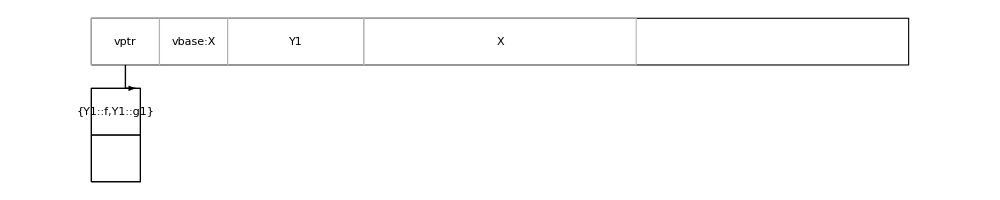

```mathematica
DrawClassDiagram[layoutY1]
```

```mathematica
layoutY2 = ComputeClassLayout[classes,"Y2"];
```

Part::partd: Part specification Bases⟦1⟧ is longer than depth of object.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[«1»,::].

Join::heads: Heads List and CppClassLayoutParser`Private`cls at positions 1 and 2 are expected to be the same.

Part::partd: Part specification Bases⟦1⟧ is longer than depth of object.

Part::partd: Part specification Bases⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[«1»,::].

General::stop: Further output of StringSplit::strse will be suppressed during this calculation.

Join::heads: Heads List and CppClassLayoutParser`Private`cls at positions 1 and 2 are expected to be the same.

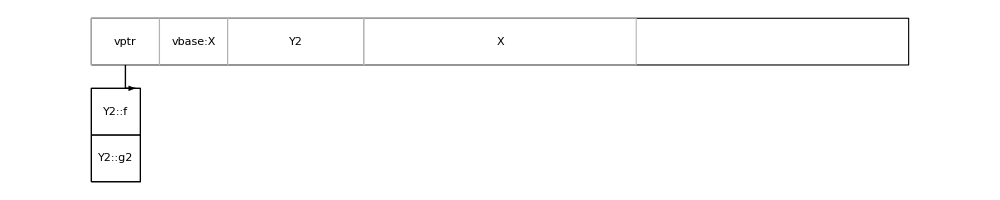

```mathematica
DrawClassDiagram[layoutY2]
```

```mathematica
layoutZ= ComputeClassLayout[classes,"Z"];
```

FilterRules::rep: <|Name→vptr,Kind→Vptr,Offset→0,Size→8,ClassOfVtable→Y1,VTableEntries→{Y1::f,Y1::g1,X::g2}|> is not a valid replacement rule.

FilterRules::rep: <|Name→vbase:X,Kind→VbaseSlot,Offset→8,Size→8,IsVirtualBase→True,VBaseOf→X|> is not a valid replacement rule.

FilterRules::rep: <|Name→vptr,Kind→Vptr,Offset→0,Size→8,ClassOfVtable→Y2,VTableEntries→{Y2::f,Y2::g2}|> is not a valid replacement rule.

General::stop: Further output of FilterRules::rep will be suppressed during this calculation.

```mathematica
layoutZ[]
```

<|ClassName→Z,Subobjects→{<|Name→vptr,Kind→Vptr,Offset→0,Size→8,ClassOfVtable→Z,VTableEntries→{Z::f,Z::g1,Y2::g2}|>,<|Name→vbase:X,Kind→VbaseSlot,Offset→8,Size→8,IsVirtualBase→True,VBaseOf→X|>,<|Name→vptr,Kind→Vptr,Offset→16,Size→8,<|Name→vptr,Kind→Vptr,Offset→0,Size→8,ClassOfVtable→Y1,VTableEntries→{Y1::f,Y1::g1,X::g2}|>→Except[{Name,Kind,Offset,Size}]|>,<|Name→vbase:X,Kind→VbaseSlot,Offset→24,Size→8,<|Name→vbase:X,Kind→VbaseSlot,Offset→8,Size→8,IsVirtualBase→True,VBaseOf→X|>→Except[{Name,Kind,Offset,Size}]|>,<|Name→vptr,Kind→Vptr,Offset→136,Size→8,<|Name→vptr,Kind→Vptr,Offset→0,Size→8,ClassOfVtable→Y2,VTableEntries→{Y2::f,Y2::g2}|>→Except[{Name,Kind,Offset,Size}]|>,<|Name→vbase:X,Kind→VbaseSlot,Offset→144,Size→8,<|Name→vbase:X,Kind→VbaseSlot,Offset→8,Size→8,IsVirtualBase→True,VBaseOf→X|>→Except[{Name,Kind,Offset,Size}]|>,<|Name→Z,Kind→Class,Offset→248,Size→24|>,<|Name→X,Kind→VirtualBase,Offset→272,Size→32,IsVirtualBase→True|>},TotalSize→336,MaxAlign→8,VTableEntries→{Z::f,Z::g1,Y2::g2}|>

```mathematica
layoutZ["Subobjects"]
```

{<|Name→vptr,Kind→Vptr,Offset→0,Size→8,ClassOfVtable→Z,VTableEntries→{Z::f,Z::g1,Y2::g2}|>,<|Name→vbase:X,Kind→VbaseSlot,Offset→8,Size→8,IsVirtualBase→True,VBaseOf→X|>,<|Name→vptr,Kind→Vptr,Offset→16,Size→8,<|Name→vptr,Kind→Vptr,Offset→0,Size→8,ClassOfVtable→Y1,VTableEntries→{Y1::f,Y1::g1,X::g2}|>→Except[{Name,Kind,Offset,Size}]|>,<|Name→vbase:X,Kind→VbaseSlot,Offset→24,Size→8,<|Name→vbase:X,Kind→VbaseSlot,Offset→8,Size→8,IsVirtualBase→True,VBaseOf→X|>→Except[{Name,Kind,Offset,Size}]|>,<|Name→vptr,Kind→Vptr,Offset→136,Size→8,<|Name→vptr,Kind→Vptr,Offset→0,Size→8,ClassOfVtable→Y2,VTableEntries→{Y2::f,Y2::g2}|>→Except[{Name,Kind,Offset,Size}]|>,<|Name→vbase:X,Kind→VbaseSlot,Offset→144,Size→8,<|Name→vbase:X,Kind→VbaseSlot,Offset→8,Size→8,IsVirtualBase→True,VBaseOf→X|>→Except[{Name,Kind,Offset,Size}]|>,<|Name→Z,Kind→Class,Offset→248,Size→24|>,<|Name→X,Kind→VirtualBase,Offset→272,Size→32,IsVirtualBase→True|>}

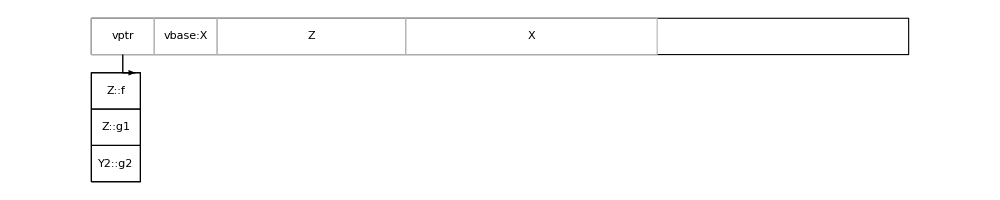

```mathematica
DrawClassDiagram[layoutZ]
```

```mathematica
Quit[]
```